# fit_malus.nb

## Least squares fit to the Malus' law.

Version of 12 Apr 2010 (Sasa)

## 1. Data

```mathematica
angles=(2π)/360 Range[0,180,10]//N
```

{0.,0.174533,0.349066,0.523599,0.698132,0.872665,1.0472,1.22173,1.39626,1.5708,1.74533,1.91986,2.0944,2.26893,2.44346,2.61799,2.79253,2.96706,3.14159}

```mathematica
amplitudes={96.3,75.8,53.5,32.7,16.5,5.1,1.5,5.2,15.5,32.3,53.0,74.4,95.0,112.7,123.7,128.9,124.2,113.6,97.0};
```

```mathematica
data=Transpose@{angles,amplitudes};
```

```mathematica
n=Length[data]
```

19

## 2. Model

```mathematica
params={pperp,ppar,x0}
```

{pperp,ppar,x0}

```mathematica
modelfn[x_,{pperp_,ppar_,x0_}]:=pperp+ppar Cos[x-x0]^2
```

```mathematica
s2fn[data_,params_]:=Module[{m,d,x=First/@data,y=Last/@data},
m=modelfn[#,params]&/@x;
d=y-m;
d.d
]
```

```mathematica
m=Length[params]
```

3

## 3. Fit

```mathematica
FindFit[data,{modelfn[x,params],pperp≥0,ppar≥0,0≤x0<2π},params,x]
```

{pperp→1.07599,ppar→126.767,x0→2.62239}

```mathematica
D[s2fn[data,params],#]&/@params/.%
```

{0.00293712,-0.00560526,-2.48597}

```mathematica
{a,b,c}=PseudoInverse[{1,Cos[2#],Sin[2#]}&/@(First/@data)].Last/@data;
pfit={pperp->a-√(b^2+c^2),ppar->2 √(b^2+c^2),x0->ArcTan[b,c]/2}
```

{pperp→1.07512,ppar→126.768,x0→-0.519199}

```mathematica
D[s2fn[data,params],#]&/@params/.pfit//N
```

{7.10543×10^-13,4.02789×10^-13,2.42721×10^-11}

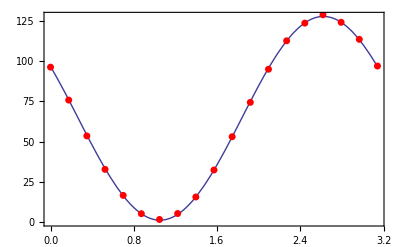

```mathematica
Plot[modelfn[x,params/.pfit],{x,Min[First/@data],Max[First/@data]},PlotStyle->Thick,Frame->True,Epilog->{Red,AbsolutePointSize[5],Point/@Transpose@{First/@data,Last/@data}}]
```

## 4. Parameter errors

```mathematica
s2min=s2fn[data,params/.pfit]
```

3.23866

```mathematica
rms=√(s2min/(n-m))
```

0.449907

```mathematica
atamat=1/2 Outer[D[(n-m)/s2min s2fn[data,params],#1,#2]&,params,params]/.pfit//N
```

{{93.866,48.1868,539.594},{48.1868,36.1543,406.746},{539.594,406.746,773463.}}

```mathematica
covmat=Inverse[atamat]
```

{{0.0337359,-0.0449649,1.10648×10^-7},{-0.0449649,0.0877552,-0.0000147794},{1.10648×10^-7,-0.0000147794,1.30058×10^-6}}

```mathematica
pstderr=Table[covmat[[i,i]],{i,m}]//Sqrt
```

{0.183673,0.296235,0.00114043}

## 5. Summary

```mathematica
MapThread[Print[StringJoin[#1," = ",#2," +/- ",#3]]&,Map[ToString,{params,params/.pfit,pstderr},{2}]];
```

pperp = 1.07512 +/- 0.183673

ppar = 126.768 +/- 0.296235

x0 = -0.519199 +/- 0.00114043